# Implementation of Sessie as an Association:

## SSSInitialize, SSSSingleStep, SSSEvolve, SSSDisplay, and SSSInteractiveDisplay all take and/or return an SSS Association ( <|...|> ).

```mathematica
Clear[FromAlpha,ToAlpha,SSSConvert, SSSStrip]; 
FromAlpha[string_String] :=(ToCharacterCode[string]-65);  
ToAlpha[l:{___Integer}] := FromCharacterCode[l+65];

Attributes[s]=Flat;
SSSConvert[string_String] := s @@ FromAlpha[string];
SSSConvert[s[x___]] := ToAlpha[{x}];
SSSConvert::usage="Converts SSS (sequential substitution system) states between s- and string-formats, using the functions FromAlpha and ToAlpha.";

SSSStrip[x_s] := SSSConvert[x⟦All,1⟧] /; MatrixQ[List@@x]    (* if dim=2, take only 1st component, and convert *)
SSSStrip[x_s] := ""  /; Length[List@@x]==0     (* treat empty string case *) 

SSSStrip::usage="SSSStrip[StyleBox[\"state\",FontSlant->\"Italic\"]] strips out tags from a StyleBox[\"state\",FontSlant->\"Italic\"] given in tagged SSS (sequential substitution system) format and returns it in string format.";
```

```mathematica
Clear[ToCharacterWeights, FromCharacterWeights, StringWeight, RuleSetWeight, RuleSetLength];
ToCharacterWeights[s_String] := (1+FromAlpha[s]);
FromCharacterWeights[l:{___Integer}] := ToAlpha[l-1];
(* Note: To avoid breaking the ruleset (un-)rank functions, avoid the temptation to define:  
ToCharacterWeights[""] = 0;  FromCharacterWeights[{0}]="";  *)
StringWeight[s_String] := Plus @@ ToCharacterWeights[s];
RuleSetWeight[rs_List] := Plus @@ (StringWeight /@ Flatten[rs /. Rule->List]);
RuleSetLength[rs_List] := Plus @@ (StringLength /@ Flatten[rs /. Rule->List]);
```

```mathematica
Clear[myColorOptions,patternPrint,SSSRuleIcon];
myColorOptions[maxColor_Integer (* minimum 1 *) ]:=Sequence[ColorRules->{0->LightGray},
ColorFunction->(Hue[(#-1)/(Max[1,maxColor])]&),ColorFunctionScaling->False];
patternPrint[pattern_,mxClr_Integer,opts___] := ArrayPlot[{{##}}& @@pattern,myColorOptions[mxClr],Mesh->True,opts,ImageSize->{Automatic,20}];
SSSRuleIcon[(rule_String|rule_Rule|rule_RuleDelayed),x___]:=SSSRuleIcon[{rule},x];

SSSRuleIcon[rules_List,x___]:=SSSRuleIcon[Map[SSSConvert,rules,{-1}],x] /; !FreeQ[rules,_String,Infinity];

SSSRuleIcon[rules_List,mxClr_Integer:6,opts___] := Panel[Grid[Map[patternPrint[#,mxClr,opts]&,rules,{2}] /. 
{Rule[x_,y_]:>{x,"→",y},RuleDelayed[x_,y_]:>{x,":>",y}}, (* invisible AlignmentMarkers! *)
Alignment->Left],"Substitution Rule"<>If[Length[rules]>1,"s:",":"]] /; FreeQ[rules,_String,Infinity];
SSSRuleIcon::usage="SSSRuleIcon[StyleBox[\"rule\",FontSlant->\"Italic\"]StyleBox[\"(\",FontSlant->\"Italic\"]StyleBox[\"s\",FontSlant->\"Italic\"]StyleBox[\")\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"maxColor\",FontSlant->\"Italic\"]] generates an icon for a sequential substitution system (SSS) rule or set of rules.";
```

```mathematica
Clear[SSSNewRule];
SSSNewRule[rulenum_Integer,(rule_Rule | rule_RuleDelayed)] := 
(* the tagged rule created will need valid versions of $SSSConnectionList, $SSSTagIndex, $SSSRulesUsed, and will change them!  It's up to the calling routine to load/unload these globals.  *)
Module[{lhs,rhs,lhsNames,newlhs,newrhs1,newrhs2},
{lhs,rhs}=List@@rule;
lhsNames = Table[Unique[lhsTag],{StringLength[lhs]}];
newlhs=ToString[s@@Transpose[{FromAlpha[lhs],ToString@#<>"_"& /@ lhsNames}]];
newrhs1=("AppendTo[$SSSConnectionList, "<>ToString[lhsNames]<>" → $SSSTagIndex + "<>ToString[Range@StringLength@rhs-1]<>"]; ");
newrhs2=ToString[SSSConvert[rhs] /. n_Integer :> {n,"$SSSTagIndex++"}];
ToExpression[newlhs<>" :> ("<>"AppendTo[$SSSRulesUsed,"<>ToString@rulenum<>"];"<>newrhs1<>newrhs2<>")"]];
SSSNewRule[rules_List] := Append[MapIndexed[SSSNewRule[First[#2],#1]&,rules],___:>AppendTo[$SSSRulesUsed,0]];
SSSNewRule::usage= 
"SSSNewRule[rule(s)] generates the needed rules for the tagged SSS (sequential substitution system) from the ruleset of rules given in string-format: e.g., \"BA\"→\"ABA\"";
```

```mathematica
Clear[SSSInitialize];
Options[SSSInitialize]={Mode->Silent};
SyntaxInformation[SSSEvolve]={"ArgumentsPattern"->{OptionsPattern[]}};

SSSInitialize::usage = "StyleBox[\"variable\",FontSlant->\"Italic\"] = SSSInitialize[ruleset, string, (mode)] attempts to perform the necessary initializion steps to generate sequential substitution system (SSS) evolutions and networks,\nstarting with a ruleset (e.g., {\"BA\"→\"ABA\"}) and an initial state string (e.g., \"BABA\").  The True|False return value indicates whether initialization was successful.\n\nIf omitted, mode defaults to \"Silent\", suppressing the short error or success message.\n\nThe following global variables are reset by this operation:\n\n$SSSNet:\t\t\t\tthe causal network of the current SSS,\n$SSSInDegree:\t\t\tthe list of in-degrees for each node,\n$SSSOutDegreeActual:\t\tthe list of currently found out-degrees for each node,\n$SSSOutDegreePotential:\t\tthe list of maximum possible out-degrees for each node,\n$SSSOutDegreeRemaining:\tthe list of numbers of possible remaining out-connections for each node,\n$SSSConnectionList:\t\tthe current list of all causal network connections,\n$SSSDistance:\t\t\tthe list of minimum distances from the current node back to the starting node.\n$SSSTagIndex:\t\t\tthe current tag index being used,\n$SSSTEvolution:\t\t\tthe complete evolution of the tagged SSS so far,\n$SSSEvolution:\t\t\tthe stripped (tagless) version of $SSSTEvolution,\n$SSSRuleSet:\t\t\tthe ruleset used for creating the SSS,\n$SSSTRuleSet:\t\t\tthe version of $SSSRuleSet (created by the function SSSNewRule) used to build $SSSTEvolution,\n$SSSRuleSetWeight:\t\tthe total weight of $SSSRuleSet,\n$SSSRuleSetLength:\t\tthe total length of $SSSRuleSet,\n$SSSRulesUsed:\t\tthe list of rules used\n$SSSCellsDeleted:\t\tthe list of cells in the state string deleted at each step,\n$SSSVerdict:\t\t\tset to \"Dead\" | \"Repeating\" as soon as the future of the SSS becomes clear.";

SSSInitialize[rs:{___Rule},state_String,opts:OptionsPattern[] (* Mode -> Silent | Quiet | Loud *)] :=
Module[{ans=<|"Net"->{},"OutDegreePotential"->{},"OutDegreeRemaining"->{},"OutDegreeActual"-> {},
"InDegree"-> {},"ConnectionList"->{},"Verdict"->"OK", "RulesUsed"->{},"CellsDeleted"->{},
"Distance"->{0}|>}, (* initial setup *)
AssociateTo[ans,{
"MaxColor"->Max[Flatten[{6,ToCharacterWeights /@ Flatten[rs/.Rule->List]}]],
"TagIndex"->StringLength[state]+1,
"TEvolution"->{s@@Transpose[{#,Range[Length[#]]}& @ FromAlpha[state]]},
"Evolution"->{state}, "RuleSet"->rs, "TRuleSet"->SSSNewRule[rs],
"RuleSetWeight"->RuleSetWeight[rs], "RuleSetLength"->RuleSetLength[rs]
}];

{$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed}={ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]};
AppendTo[ans["TEvolution"],Last[ans["TEvolution"]]/.ans["TRuleSet"]];
{ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]}={$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed};

Switch[ Last[ans["RulesUsed"]], (* can also test if Length[ans["ConnectionList"]]==0 *)
0,ans["TEvolution"]=Most[ans["TEvolution"]]; (* toss last duplicate entry *)
      ans["Verdict"]="Dead";
      If[ OptionValue[Mode]==Loud,Print["Error: No evolution possible starting from \""<>state<>"\" using ruleset: ",rs]];
      Return[ans (* but already including "Verdict" = Dead *)],
_, AppendTo[ans["Evolution"],SSSStrip[Last[ans["TEvolution"]]]]; (* add last entry *)
       If[ OptionValue[Mode]==Loud,Print["Successful initialization of ruleset: ",rs,", evolution: ",ans["Evolution"]]]
];
(* updateDegrees: this code needed for both SSSInitialize and SSSSingleStep *)
AppendTo[ans["InDegree"],Length[ans["ConnectionList"]⟦-1,1⟧]];  (* # cells killed by this event = in-degree *)
(* calculate potential outdegree of new event, append to list *)
AppendTo[ans["OutDegreePotential"],Length[ans["ConnectionList"]⟦-1,-1⟧]]; (* # of cells created by last rule *)
AppendTo[ans["OutDegreeRemaining"],Last[ans["OutDegreePotential"]]];
AppendTo[ans["OutDegreeActual"],0];
AppendTo[ans["CellsDeleted"],Flatten[Position[ans["TEvolution"]⟦-2⟧,{_,#}]& /@ans["ConnectionList"]⟦-1,1⟧]];  (* Note positions of entries with tags indicated, add to the list *)
(* end of duplicate code *)

ans  (* Return the association created *)
];
```

```mathematica
Clear[SSSSingleStep];
SSSSingleStep::usage=
"SSSSingleStep[sss] performs a single step of the sequential substitution system sss evolution (if not already dead), returning the sss object (which must be created by SSSInitialize first).";

SSSSingleStep[sss_Association] := Module[{ans=sss,cd, ri, pri, rs, prs,len,startingEvents, oda, odr},
If[ans["Verdict"]==="Dead",Return[ans]];  (* if already dead, do nothing, return *)

(* do the actual evolution step *)
{$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed}={ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]};
AppendTo[ans["TEvolution"],Last[ans["TEvolution"]]/.ans["TRuleSet"]];
{ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]}={$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed};

If[Last[ans["RulesUsed"]]==0,ans["Verdict"]="Dead"; 
ans["TEvolution"]=Most[ans["TEvolution"]]; 
Return[ans]
];

AppendTo[ans["Evolution"],SSSStrip[Last[ans["TEvolution"]]]];

If[!MatchQ[ans["Verdict"],"Repeating"],  (* to limit wasted time, don't do this if the verdict is already in! *)
If[Length[Flatten@Position[ans["Evolution"],Last[ans["Evolution"]]]]>1, ans["Verdict"]="Repeating"]
]; 

(* updateDegrees: this code needed for both SSSInitialize and SSSSingleStep *)
AppendTo[ans["InDegree"],Length[ans["ConnectionList"]⟦-1,1⟧]];  (* # cells killed by this event = in-degree *)
(* calculate potential outdegree of new event, append to list *)
AppendTo[ans["OutDegreePotential"],Length[ans["ConnectionList"]⟦-1,-1⟧]]; 
AppendTo[ans["OutDegreeRemaining"],Last[ans["OutDegreePotential"]]];
AppendTo[ans["OutDegreeActual"],0];
AppendTo[ans["CellsDeleted"],Flatten[Position[ans["TEvolution"]⟦-2⟧,{_,#}]& /@ans["ConnectionList"]⟦-1,1⟧]];  (* Note positions of entries with tags indicated, add to the list *)
(* end of duplicate code *)

(* now the steps that are only done for non-initial steps, comparing to previous entries in ans["ConnectionList"]: *)
len=Length[ans["ConnectionList"]];
startingEvents=Flatten[If[Length[#]>0,First[First[#]],#]& /@ (Position[ans["ConnectionList"]⟦;;-2⟧,#]& /@ ans["ConnectionList"]⟦-1,1⟧)];
oda=ans["OutDegreeActual"];
oda⟦#⟧++& /@ startingEvents; (* update out-degee list for events involved *)
AssociateTo[ans,"OutDegreeActual"->oda];
odr=ans["OutDegreeRemaining"];
odr⟦#⟧--& /@ startingEvents; (* update out-degee list for events involved *)
AssociateTo[ans,"OutDegreeRemaining"->odr];
AssociateTo[ans,"Net"->Join[ans["Net"],#->len& /@ startingEvents]];           (* add new links to the causal network *)
AssociateTo[ans,"Distance"->Append[ans["Distance"],Min[ans["Distance"]⟦startingEvents⟧]+1]];  (* Find minimum path length of cause nodes, add 1 for path lengths of result nodes *)

ans  (* Return the updated association *)
];
```

```mathematica
Clear[SSSEvolve];
Options[SSSEvolve]={EarlyReturn->False, Mode->Silent};
SyntaxInformation[SSSEvolve]={"ArgumentsPattern"->{OptionsPattern[]}};

SSSEvolve[sss_Association,n_Integer/;n>0,opts:OptionsPattern[]] := Module[{ans=sss},
If[OptionValue[EarlyReturn] ,
Do[If[MatchQ[ans["Verdict"], ("Dead"|"Repeating")],Return[ans],ans=SSSSingleStep[ans]],{n}], (* check before each step *)
Do[ans=SSSSingleStep[ans],{n}]   (* just do it *)
];
If[OptionValue[Mode]==Loud,Print[ans["Verdict"]]];
ans
]
```

```mathematica
SSSEvolve::usage="SSSEvolve[sss, n] generates an additional n levels of indicated sss (sequential substitution system), which must have been previously created using SSSInitialize.  Use the option EarlyReturn → True to allow early termination for repeating cases.  (SSSSinglestep immediately returns anyway if the SSS is dead.)  In Loud mode, prints the current verdict, \"OK\" means none known.  Values of sss updated, with \"Evolution\" containing the tagless SSS, \"ConnectionList\" the updated causal network connection list, etc.  mode can be Silent, Quiet, or Loud.";
```

```mathematica
Clear[SSSDisplay];
Options[SSSDisplay]=
{HighlightMethod->True,RulePlacement->Bottom,Mesh->True,NetSize->{Automatic,400},SSSSize->{Automatic,300},IconSize->{Automatic,20},ImageSize->Automatic,NetMethod->GraphPlot,
Max->∞,SSSMax->Automatic,NetMax->Automatic,
Min->1,SSSMin->Automatic,NetMin->Automatic, 
Sequence@@Union[Options[TreePlot],Options[GraphPlot],Options[GraphPlot3D],Options[LayeredGraphPlot]]};
SyntaxInformation[SSSDisplay]={"ArgumentsPattern"->{OptionsPattern[]}};
```

```mathematica
SSSDisplay[sss_Association, opts:OptionsPattern[]] := Module[{HlM,mesh,IcS,ImS,SS,NS,RP,NM,doGP,doLGP,doTP,doGP3D,doSSS,myNet,ans,cellsToHighlight,rulesApplied,mx,netmx,sssmx,mn,netmn,sssmn,hs,start,ev,vrtxs,net,grph,DE},

HlM =If[#===True,Number,#]& @ OptionValue[HighlightMethod]; 
RP=OptionValue[RulePlacement];
mesh=OptionValue[Mesh];
SS = OptionValue[SSSSize];
IcS = OptionValue[IconSize];
ImS = OptionValue[ImageSize];
NS = OptionValue[NetSize];
NM=OptionValue[NetMethod];
DE= OptionValue[DirectedEdges];

mx=OptionValue[Max];
If[mx===Automatic,mx=∞];
sssmx=OptionValue[SSSMax]; 
If[sssmx===Automatic,sssmx=mx];
netmx=OptionValue[NetMax]; 
If[netmx===Automatic,netmx=mx];

mn=OptionValue[Min];
If[mn===Automatic,mn=1];
sssmn=OptionValue[SSSMin]; 
If[sssmn===Automatic,sssmn=mn];
netmn=OptionValue[NetMin]; 
If[netmn===Automatic,netmn=mn];

start=1;

vrtxs =Annotation[#,VertexWeight->sss["Distance"]⟦#⟧]&/@Range[Max[start,netmn],Min[netmx,Length[sss["Distance"]]]];

net=(Select[sss["Net"],And@@Thread[Max[start,netmn]≤List@@#≤netmx]&] /. n_Integer:>(n+1-start));

(*
If[UD||(DM<∞),net=(net /.nn_Integer:>Subscript[sss["Distance"]⟦nn⟧,Style[nn,Tiny]])];
If[DM<∞,
net=Cases[net,r:Rule[Subscript[_?(#≤DM&),_],Subscript[_?(#≤DM&),_]]:> r];
If[!UD,net=(net /. Subscript[_,Style[n_Integer,_]]:>n)]
];
*)

grph=Graph[vrtxs,net,DirectedEdges->DE];

doGP=doLGP=doTP =doGP3D=False;doSSS=True;
If[MemberQ[NM,All,{0,∞}],doGP=doLGP=doTP=doGP3D=True];
If[MemberQ[NM,GraphPlot,{0,∞}],doGP=True];
If[MemberQ[NM,LayeredGraphPlot,{0,∞}],doLGP=True];
If[MemberQ[NM,TreePlot,{0,∞}],doTP=True];
If[MemberQ[NM,GraphPlot3D,{0,∞}],doGP3D=True];
If[MemberQ[NM,NoSSS,{0,∞}],doSSS=False];

If[sss["Verdict"]=="Dead",doGP=doLGP=doTP=doGP3D=False];

cellsToHighlight=Flatten[MapIndexed[{#1,#2⟦1⟧}&,Reverse@(sss["CellsDeleted"]⟦Max[start,sssmn];;Min[sssmx,Length[sss["Evolution"]]]-1⟧),{2}],1];
rulesApplied=Reverse@(sss["RulesUsed"]⟦Max[start,sssmn];;Min[sssmx,Length[sss["Evolution"]]]-1⟧);

ans = 
ArrayPlot[(FromAlpha/@ (sss["Evolution"]⟦Max[start,sssmn];;Min[sssmx,Length[sss["Evolution"]]]⟧)),myColorOptions[sss["MaxColor"]],Mesh->mesh,ImageSize->SS,
Epilog->Switch[HlM,
Dot,Disk[#+0.5{-1,1},.18]& /@ cellsToHighlight,
Frame,{EdgeForm[Thick],FaceForm[],Rectangle[#-{1,0}]& /@ cellsToHighlight},
Number,Text @@@ (cellsToHighlight /. {x_Integer,y_Integer}:>{rulesApplied⟦y⟧,{x,y}+.5{-1,1}}),
_,{}]
];
Row[Flatten@{
If[!doSSS,{},Pane[
Switch[RP,
Right, Grid[{{ans,SSSRuleIcon[sss["RuleSet"],sss["MaxColor"],ImageSize->IcS]}}],
Left, Grid[{{SSSRuleIcon[sss["RuleSet"],sss["MaxColor"],ImageSize->IcS],ans}}], 
Bottom|True, Grid[{{ans},{SSSRuleIcon[sss["RuleSet"],sss["MaxColor"],ImageSize->IcS]}}], 
Top,  Grid[{{SSSRuleIcon[sss["RuleSet"],sss["MaxColor"],ImageSize->IcS]},{ans}}], 
_,ans],ImageSize->ImS,ImageSizeAction->"ShrinkToFit"]],
If[doGP,GraphPlot[grph,GraphLayout->"SpringElectricalEmbedding",
Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot]],
VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}],
If[doLGP,LayeredGraphPlot[grph,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[LayeredGraphPlot]],VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}],
If[doTP,TreePlot[grph,Top,1,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[TreePlot]],VertexSize->Large,VertexLabels->Placed[Automatic,Center],DirectedEdges->True}]],{}],
If[doGP3D,GraphPlot3D[grph,GraphLayout->"SpringElectricalEmbedding",Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot3D]],VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}]
},"  "]]
```

```mathematica
SSS[rs:{___Rule},init_String,n_Integer?Positive,opts___] := Module[{sss},
sss=SSSInitialize[rs,init,Mode->Silent];
If[sss["Verdict"]=!="Dead", 
sss=SSSEvolve[sss,n-1,Sequence@@FilterRules[{opts},Options[SSSEvolve]]]; 
Print@SSSDisplay[sss,Sequence@@FilterRules[{opts},Options[SSSDisplay]]];
];
sss
];
Options[SSS]=Join[Options[SSSEvolve],Options[SSSDisplay]];
SyntaxInformation[SSS]={"ArgumentsPattern"->{_,_,_,OptionsPattern[]}};
```

```mathematica
SSS::usage="SSS[rule, init, n, opts] creates and displays a sequential substitution system (SSS) and its causal network, using ruleset starting with the state init (using string notation), allowing the SSS to evolve for n steps.  Use the option EarlyReturn to give/deny permission to quit early if the SSS can be identified as dead or (pseudo-)repeating.)  Any other options given are passed on to SSSDisplay.

(Returns a copy of the SSS that can then be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly, looking at its keys, \"Evolution\" and \"Net\", etc.)";
```

```mathematica
Clear[SSSInteractiveDisplay,dynamicLabel];

dynamicLabel[lbl_,max_]:=Dynamic[If[Clock[{1,max,1},max]==lbl,Framed[lbl,Background->Green,RoundingRadius->Scaled[.5]],lbl]];

SetAttributes[SSSInteractiveDisplay,HoldFirst];

SSSInteractiveDisplay[sss_] := With[{mxmx=Max[List @@@ Evaluate[sss]["Net"]]},
Manipulate[
If[Head[vl]===List,vp=Automatic];
If[mx<mn,mx=mn+1];
If[sssmx<sssmn,sssmx=sssmn+1];
If[ntmx<ntmn,ntmx=ntmn+1];
args={Min->mn,Max->mx,SSSMin->(sssmn/. 0->Automatic),SSSMax->(sssmx/. mxmx+1->Automatic),NetMin->(ntmn/. 0->Automatic),NetMax->(ntmx/.mxmx+1->Automatic),HighlightMethod->hlm,RulePlacement->sr,NetMethod->Flatten[{nm,If[no,{NoSSS},{}]}],ImageSize->is,NetSize->{Automatic,ns},SSSSize->{Automatic,ssss},IconSize->{Automatic,cns},VertexSize->vs,
VertexLabels->If[vp===Automatic,vl,Placed[vl,vp]],
DirectedEdges->dir};
SSSDisplay[Evaluate[sss],Flatten[args,1]],
Grid[{{
Control[{{hlm,Number,"HighlightMethod"},{Dot,Frame,Number,None}}],
Control[{{sr,Bottom,"RulePlacement"},{Bottom,Top,Left,Right,None}}],
Control[{{nm,GraphPlot,"NetMethod"},{GraphPlot,LayeredGraphPlot,TreePlot,GraphPlot3D,All}}],
Button["Save these options",
CellPrint[ExpressionCell[Defer[SSSDisplay][Defer[sss],Evaluate[Sequence@@args]],"Input"]];
SelectionMove[InputNotebook[],Previous,Cell];
]
}},Spacings->2],
{args,{},ControlType->None},
Grid[{{Control[{{mn,1,"Min"},1,mxmx,1,Appearance->"Labeled"}],Control[{{mx,mxmx,"Max"},1,mxmx,1,Appearance->"Labeled"}],
Row[{
Control[{{dir,False,"directed"},{False,True}}],"    ",
Control[{{no,False,"NoSSS"},{False,True}}]
}]
},
{Control[{{sssmn,0,"SSSMin"},0,mxmx,1,Appearance->"Labeled"}],Control[{{sssmx,mxmx+1,"SSSMax"},0,mxmx+1,1,Appearance->"Labeled"}],"(a NetMethod option)"},{Control[{{ntmn,0,"NetMin"},0,mxmx,1,Appearance->"Labeled"}],Control[{{ntmx,mxmx+1,"NetMax"},0,mxmx+1,1,Appearance->"Labeled"}],
Control[{{vs,Automatic,"VertexSize →"},{Automatic,Tiny,Small,Medium,Large,0.8->"Huge"},ControlType->PopupMenu}]
},
{Control[{{ssss,220,"SSSSize"},10,500,Appearance->"Labeled"}],
Control[{{is,350,"ImageSize"},10,500,Appearance->"Labeled"}],Control[{{vl,Automatic,"VertexLabels →"},{Automatic,None,"Name","VertexWeight",
((#->Placed[#,Center,Function[{arg},dynamicLabel[arg,ntmx]]])&/@Range[ntmn+1,ntmx-1])->"Dynamic"},ControlType->PopupMenu}]},
{Control[{{cns,20,"IconSize"},10,50,Appearance->"Labeled"}],Control[{{ns,300,"NetSize"},10,800,Appearance->"Labeled"}],
Control[{{vp,Automatic,"Placed"},
{Automatic,Center,Before,After,Below,Above,Tooltip,StatusArea}}]}
},Alignment->Right,Spacings->2]
]]
SSSInteractiveDisplay::usage="SSSInteractiveDisplay[sss] provides an interactive display of sss and its causal network, with controls for easy adjustment of common options.  Click the button to create a SSSDisplay object with the selected options.";
```

## If everything above loaded correctly, the following lines will work:


-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
SSSRuleIcon[{"A"->"B",""->"A"}]
```

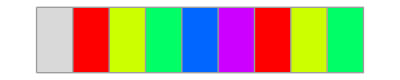
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
SSSRuleIcon[{"A"->"B",""->"ABCDEFGHI"}]
```

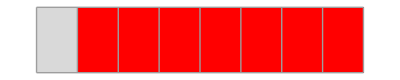
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
SSSRuleIcon[{"A"->"B",""->"ACDEFGHI"},2] (* Fixed so it doesn't take less than 2 colors, default is 6,  Note: color 0 = LightGray, not part of the cycle if colors are repeated! *)
```

```mathematica
SSSNewRule[{"ABA"->"AAB","A"->"ABA"}]
```

Create and initialize a sessie object, look at different fields, use SSSSingleStep, SSSEvolve, SSSDisplay on it:

```mathematica
sss=SSSInitialize[{"ABA"->"AAB","A"->"ABA"}, "A"];
Normal[sss]//Column
```

Net→{}
OutDegreePotential→{3}
OutDegreeRemaining→{3}
OutDegreeActual→{0}
InDegree→{1}
ConnectionList→{{1}→{2,3,4}}
Verdict→OK
RulesUsed→{2}
CellsDeleted→{{1}}
Distance→{0}
MaxColor→6
TagIndex→5
TEvolution→{s[{0,1}],s[{0,2},{1,3},{0,4}]}
Evolution→{A,ABA}
RuleSet→{ABA→AAB,A→ABA}
TRuleSet→{s[{0,lhsTag$6302_},{1,lhsTag$6303_},{0,lhsTag$6304_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$6302,lhsTag$6303,lhsTag$6304}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++},{1,$SSSTagIndex++}]),s[{0,lhsTag$6306_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$6306}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]}
RuleSetWeight→13
RuleSetLength→10

```mathematica
{sss["TagIndex"],sss["Evolution"]}
```

{5,{A,ABA}}

```mathematica
sss=SSSSingleStep[sss];
{sss["TagIndex"],sss["Evolution"]}
```

```mathematica
sss=SSSEvolve[sss,50];
sss["Evolution"]
```

{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB,AAABAABBB,AAAABABBB,AAAAABBBB,ABAAAAABBBB,AABAAAABBBB,AAABAAABBBB,AAAABAABBBB,AAAAABABBBB,AAAAAABBBBB,ABAAAAAABBBBB,AABAAAAABBBBB,AAABAAAABBBBB,AAAABAAABBBBB,AAAAABAABBBBB,AAAAAABABBBBB,AAAAAAABBBBBB,ABAAAAAAABBBBBB,AABAAAAAABBBBBB,AAABAAAAABBBBBB,AAAABAAAABBBBBB,AAAAABAAABBBBBB,AAAAAABAABBBBBB,AAAAAAABABBBBBB,AAAAAAAABBBBBBB,ABAAAAAAAABBBBBBB,AABAAAAAAABBBBBBB,AAABAAAAAABBBBBBB,AAAABAAAAABBBBBBB,AAAAABAAAABBBBBBB,AAAAAABAAABBBBBBB,AAAAAAABAABBBBBBB,AAAAAAAABABBBBBBB,AAAAAAAAABBBBBBBB,ABAAAAAAAAABBBBBBBB,AABAAAAAAAABBBBBBBB,AAABAAAAAAABBBBBBBB,AAAABAAAAAABBBBBBBB,AAAAABAAAAABBBBBBBB,AAAAAABAAAABBBBBBBB,AAAAAAABAAABBBBBBBB}

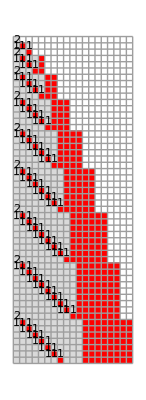


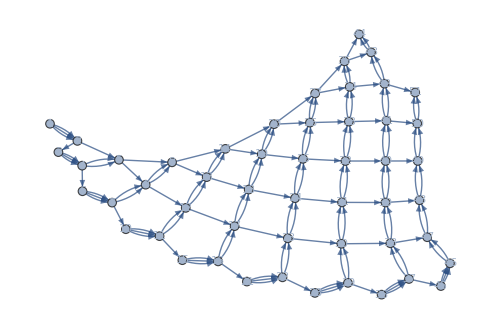
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss,NetSize->500]
```

Normal way to create, evolve, and display a sessie object:

```mathematica
sss=SSS[{"ABA"->"AAB","A"->"ABA"}, "A",44,SSSMax->15,NetMethod->GraphPlot];
```

Create another SSS without erasing the first one:

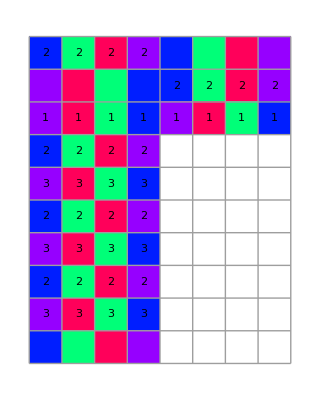
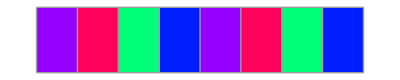
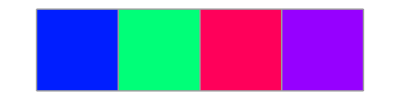
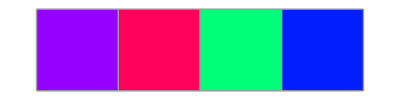
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
mirosessie = SSS[{"ORIMORIM" -> "MIRO", "MIRO" -> "ORIM", "ORIM" -> "MIRO"}, "MIROMIRO", 10, SSSMax -> 10, NetMethod -> GraphPlot, NetSize->30];
```

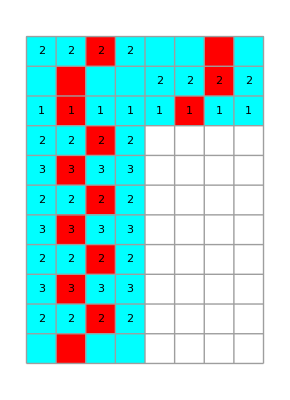
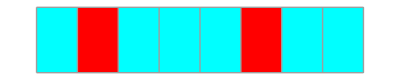
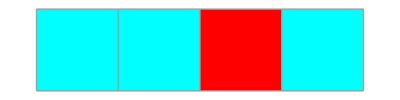
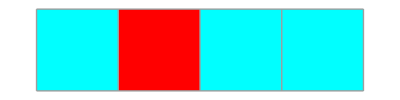
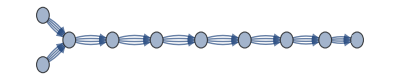
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
AssociateTo[mirosessie, "MaxColor" ->2];
SSSDisplay[mirosessie,NetSize->400]
```

```mathematica
mirosessie["Verdict"]
mirosessie["Evolution"]
mirosessie["MaxColor"]
```

1

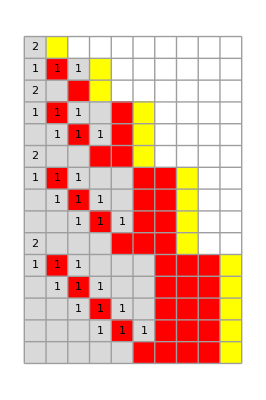
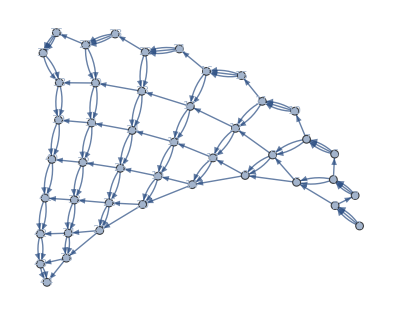
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss2=SSS[{"ABA"->"AAB","A"->"ABA"}, "AC",44,SSSMax->15,NetMethod->GraphPlot];
```

Both exist independently:

```mathematica
sss["Evolution"]
```

```mathematica
sss2["Evolution"]
```

{AC,ABAC,AABC,ABAABC,AABABC,AAABBC,ABAAABBC,AABAABBC,AAABABBC,AAAABBBC,ABAAAABBBC,AABAAABBBC,AAABAABBBC,AAAABABBBC,AAAAABBBBC,ABAAAAABBBBC,AABAAAABBBBC,AAABAAABBBBC,AAAABAABBBBC,AAAAABABBBBC,AAAAAABBBBBC,ABAAAAAABBBBBC,AABAAAAABBBBBC,AAABAAAABBBBBC,AAAABAAABBBBBC,AAAAABAABBBBBC,AAAAAABABBBBBC,AAAAAAABBBBBBC,ABAAAAAAABBBBBBC,AABAAAAAABBBBBBC,AAABAAAAABBBBBBC,AAAABAAAABBBBBBC,AAAAABAAABBBBBBC,AAAAAABAABBBBBBC,AAAAAAABABBBBBBC,AAAAAAAABBBBBBBC,ABAAAAAAAABBBBBBBC,AABAAAAAAABBBBBBBC,AAABAAAAAABBBBBBBC,AAAABAAAAABBBBBBBC,AAAAABAAAABBBBBBBC,AAAAAABAAABBBBBBBC,AAAAAAABAABBBBBBBC,AAAAAAAABABBBBBBBC,AAAAAAAAABBBBBBBBC}

Use SSSInteractiveDisplay to tweak the display options:

```mathematica
SSSInteractiveDisplay[sss]
```

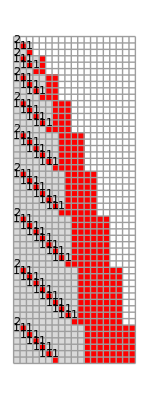
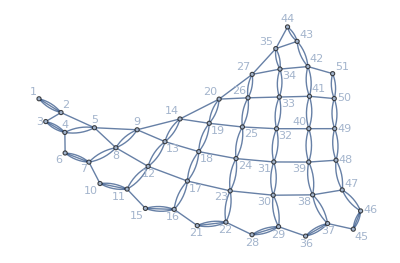
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss,Min->1,Max->51,SSSMin->Automatic,SSSMax->Automatic,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->350,NetSize->{Automatic,300},SSSSize->{Automatic,220},IconSize->{Automatic,10.},VertexSize->Automatic,VertexLabels->Automatic,DirectedEdges->False]
```